## Simulation of Classical -> Quantum harmonic oscillator

This script simulates the dynamics of a harmonic oscillator  using the classical Langevin Equation. The dynamics are described by damped oscillator subject to thermal noise from the environment :  where  and ,  is expected value of phonons. In classical limit  we get symmetrized version . We simulate this noise by simple scheme:  where  is a Gaussian random variable:
.  and .  
For start we define physical constants.

```mathematica
(*Clear previous definitions *)
ClearAll["Global`*"]

(*Physics Parameters*)
hbar = 6.62607015*^-34; (* J Hz^-1 *)
kb = 1.381*^-23;        (* m^2 kg s^-2 K^-1 *)
Tval = 0.01;            (* K *)
omegam = 2 Pi * 1000;   (* 1 kHz *)
gamma = 2 Pi * 10;      (* 1 Hz damping *)
(* Average phonons *)
(* nbar = 1 / (Exp[hbar * omegam / (kb * Tval)] - 1); *)
nbar = 1.0; (* Fixed for simplicity *)
sigma = Sqrt[gamma (nbar + 1/2)]; (* Amplitude of noise *)

Print["nbar = ", nbar];
```

nbar = 1.

For simulating dynamics we are using the Stratonovich Runge-Kutta 2nd Order (SRK2) numerical scheme. Although simpler version described above often sufficient for additive noise, SRK2 offers higher accuracy in the Stratonovich sense. The simulation is highly vectorized across nRepeats for fast execution.

```mathematica
(* Simulation Parameters*)
dt = 1.*^-5;
nSteps = 10000;
nRepeats = 100;

(* Simulation Method STK2*)
simulateSRK2[] := Module[
  {a, aPrev, k1, k2, eta, dW, driftConst, dWAll},

  a = ConstantArray[0.0 + 0.0 I, {nSteps, nRepeats}];
  
  (* Initial condition *)
  a[[1]] = ConstantArray[Sqrt[nbar], nRepeats];
  
  driftConst = (-I * omegam - gamma/2);
 
  dWAll = Sqrt[dt/2] * (
      RandomReal[NormalDistribution[0, 1], {nSteps, nRepeats}] + 
      I * RandomReal[NormalDistribution[0, 1], {nSteps, nRepeats}]
  );
  
  (* Use Do loop for time stepping *)
  Do[
    aPrev = a[[i - 1]];
    dW = dWAll[[i]];
    
    eta = RandomReal[NormalDistribution[0, 1], nRepeats] + I * RandomReal[NormalDistribution[0, 1], nRepeats];

    k1 = driftConst * aPrev;
    k2 = driftConst * (aPrev + k1 * dt + sigma * Sqrt[dt] * eta);
    
    (* SRK2 Step: a_n+1 = a_n + 0.5 * (k1 + k2) * dt + sigma * dW *)
    a[[i]] = aPrev + 0.5 * (k1 + k2) * dt + sigma * dW;
    , {i, 2, nSteps}];
  
  a
];
```

We also are interested in calculating power spectrum density. The definition of power spectrum density  where , is fourier transform over interval . Numerically we can approximate this with FFT.

```mathematica
(* Compute PSD for a single signal *)
calculatePSD[data_, dt_] := Module[{n, fs, freqs, freqsShifted, yf,yfShifted, psdShifted, psdReversed,psdSymmetric },
  n = Length[data];
  fs = 1/dt;

  yf = Fourier[data, FourierParameters -> {1, -1}];

  freqs = fs Range[0, n - 1]/n;
  freqsShifted = fs Range[-Floor[n/2], Ceiling[n/2]-1]/n;
  yfShifted = RotateLeft[yf, Floor[n/2]];
  
  psdShifted = Abs[yfShifted]^2/(n fs);
  psdReversed = Reverse[psdShifted];

  psdSymmetric = 0.5*(psdShifted + psdReversed);


  {freqsShifted, psdSymmetric}
]
(* Compute mean PSD  *)
calculateAveragePSD[dataMatrix_, dt_] := Module[{psdList, freqsShifted, avgPSD},
  psdList = Table[
     calculatePSD[dataMatrix[[All, i]], dt][[2]],
     {i, Dimensions[dataMatrix][[2]]}
  ];
  freqsShifted = calculatePSD[dataMatrix[[All, 1]], dt][[1]];
  avgPSD = Mean[psdList];
  {freqsShifted, avgPSD}
]


(* Analytic PSD Function *)
analyticPSD[f_] := Module[{w, chi},
   w = 2 Pi * f;
   chi = 1/(-I (w - omegam) + gamma/2);
   Abs[chi]^2 * (gamma * (nbar + 1/2))
];
```

Run simulation and calculate statistics

```mathematica
(* Run Simulation *)
Print["Simulating ", nRepeats, " trajectories..."];
(* time *)
{timeTaken, complexData} = AbsoluteTiming[simulateSRK2[]];
Print["Simulation time: ", timeTaken, " s"];

(* Extract X and P *)
Xss = Re[complexData];
Pss = Im[complexData];

(* Calculate Statistics *)
finalX = Xss[[-1]];
finalP = Pss[[-1]];
meanN = Mean[finalX^2 + finalP^2];

Print["Simulated <n> = ", meanN];
Print["Expected <n> + 1/2 = ", nbar + 0.5];

(* Trajectory Averages *)
xTraj = Mean /@ Xss / Sqrt[2];
pTraj = Mean /@ Pss / Sqrt[2];
timeAxis = Range[nSteps] * dt;
{freqs, psdNum} = calculateAveragePSD[complexData, dt];

Print["Theoretical integral Sxx = ", nbar + 1/2];
```

Simulating 10 trajectories...

Simulation time: 0.271936 s

Simulated <n> = 1.7429

Expected <n> + 1/2 = 1.5

Theoretical integral Sxx = 1.5

Ploting

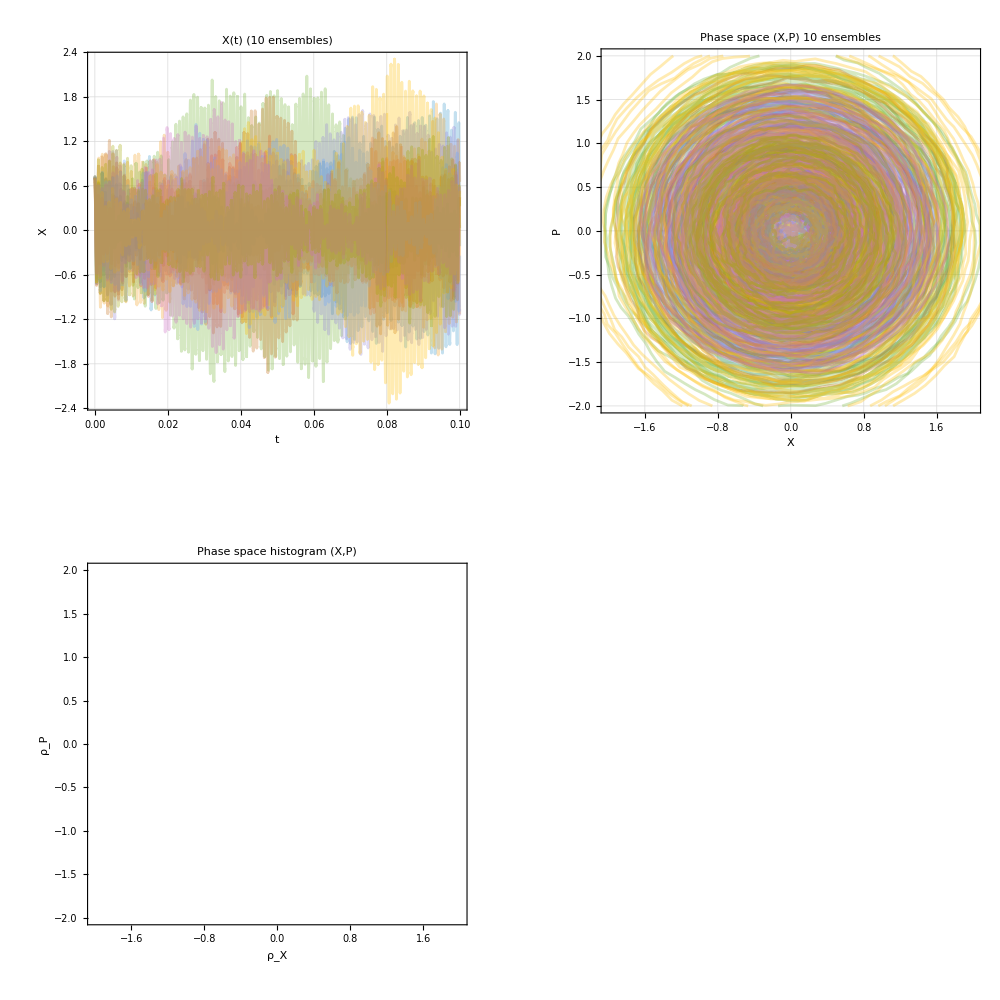

```mathematica
plot1 = ListLinePlot[
   Table[Transpose[{timeAxis, Xss[[All, i]]/Sqrt[2]}], {i, 1, 10}],
   PlotRange -> All,
   Frame -> True,
   FrameLabel -> {"t", "X"},
   PlotLabel -> "X(t) (10 ensembles)",
   PlotStyle -> Directive[Opacity[0.3]],
   GridLines -> Automatic, GridLinesStyle -> Dashed,
   AspectRatio -> 1
];

(* 2. Phase Space  *)
plot2 = ListLinePlot[
   Table[Transpose[{Xss[[All, i]]/Sqrt[2], Pss[[All, i]]/Sqrt[2]}], {i, 1, 10}],
   PlotRange -> {{-2, 2}, {-2, 2}},
   Frame -> True,
   FrameLabel -> {"X", "P"},
   PlotLabel -> "Phase space (X,P) 10 ensembles",
   PlotStyle -> Directive[Opacity[0.3]],
   AspectRatio -> 1,
   GridLines -> Automatic, GridLinesStyle -> Dashed,
   AspectRatio -> 1
];

(* 3. Histogram  *)
flatX = Flatten[Xss]/Sqrt[2];
flatP = Flatten[Pss]/Sqrt[2];
dataPairs = Transpose[{flatX, flatP}];

plot3 = DensityHistogram[dataPairs, 
   {50, 50}, 
   "PDF",
   ColorFunction -> ColorData["DeepSeaColors"], 
   PlotRange -> {{-2, 2}, {-2, 2}},
   Frame -> True,
   FrameLabel -> {"\!\(\*SubscriptBox[\(ρ\), \(X\)]\)", "\!\(\*SubscriptBox[\(ρ\), \(P\)]\)"},
   PlotLabel -> "Phase space histogram (X,P)",
   AspectRatio -> 1
];

(* 4. Power Spectral Density *)
(* Filter positive frequencies for log plot *)

posIdx = Flatten[Position[freqs, _?(# > 0 &)]];
posFreqs = Extract[freqs, List /@ posIdx];
posPSD = Extract[psdNum, List /@ posIdx];
analyticVals = analyticPSD[posFreqs];

plot4 = ListLogLogPlot[
   {
    Transpose[{posFreqs, posPSD}],
    Transpose[{posFreqs, analyticVals}]
   },
   PlotStyle -> {
     Directive[Black, Thickness[0.005]], 
     Directive[RGBColor[0.55, 0.1, 0.1], Dashed, Thickness[0.003]]
   },
   Frame -> True,
   FrameLabel -> {"frequency", "\!\(\*SubscriptBox[\(S\), \(XX\)]\)"},
   PlotLabel -> "Power density spectrum",
   GridLines -> {{omegam/(2 Pi)}, None},
   GridLinesStyle -> Directive[Orange, Dashed, Thickness[0.002]],
   PlotLegends -> Placed[{"Simulation", "Analytic"}, {0.2, 0.2}],
   AspectRatio -> 1
];

(* Combine Plots *)
GraphicsGrid[
 {{plot1, plot2}, {plot3, plot4}},
 ImageSize -> {1000, 1000},
 Spacings -> {20, 20}
]
```